# Volterra Solvers and Power Spectra -- waves, single species.

Created 2025.
Last edited March 2026.
 Email mustafa.a.amin@rice.edu if you have questions or corrections.
 
Please cite the following depending on your usage:
For particle-like DM with Warmth and Poisson :
- single species  Amin, Delos & Mirbabayi (2025)[https://arxiv.org/abs/2503.20881]. Also includes N-body simulations. More general code also available.
- multi-species, Amin, Delos & Yang (2025) [https://arxiv.org/abs/2510.15046]. Also includes (limited) N-body simulations.
For Wave DM with Warmth and Poisson:
- single species,  Amin, May & Mirbabayi (2025) [https://arxiv.org/abs/2506.12131]. Includes nonlinear Schrodinger-Poisson simulations.
- multi-species,   Amin & Delos (2025) [https://arxiv.org/abs/2510.17977]. Most general, can include the particle case also.

## parameters

```mathematica
Quit[];
```

```mathematica
(* ~~~~~~~~ Numberical Parameters ~~~~~~~~`*)
{y0,y}={10^-3.,10^3.}; (* y-range *)
{kmin,kmax}={0.5,8 10^3.}; (* k-range *)
{Ny,Nit,Nk}={300,12,60};(* # of y-divisions, Picard iterations, k samples *)
yout={0.01,0.1,1.,10.,100.,1000.}; 

(* Some relevant cosmological parameters *)
Mpc=1.;
eV=1.56 10^29 Mpc^-1;
keq=0.01 Mpc^-1;aeq=1/3388.;


(* Specify the particle mass and k* *)
m=10^-19. eV;         (* particle mass *)
ks=10^3. Mpc^-1;(* k* for the warm wave dm *)
```

## Computing the transfer functions Ta, Tb, Tc

```mathematica
(*~~~~~ pre-defined functions and grids ~~~~~~*)
(* y-Grid, y-midpoints, and k-grid *)
ygrid=Exp@Subdivide[Log[y0],Log[y],Ny-1]; (* log-spaced y-grid *)
r=(√(ygrid[[2]]/ygrid[[1]])-√(ygrid[[1]]/ygrid[[2]])); (* r = √(Subscript[y, i+1]/Subscript[y, i])-√(Subscript[y, i]/Subscript[y, i+1]) *)
midpts=√(Most[ygrid]*Rest[ygrid]); (* Subscript[m, i]=√(Subscript[y, i+1] Subscript[y, i]) of y-grid,useful for integration, (Subscript[y, i+1]-Subscript[y, i])=Subscript[y, i] r *)
Nmid=Length[midpts]; (* # of y midpoints *)
klist=Exp@Subdivide[Log[kmin],Log[kmax],Nk-1]; (*k-grid*)

(*Precompute k-independent matrices*)
F=Outer[Log[#1/#2 (1+√(1+#2))^2/(1+√(1+#1))^2]&,midpts,midpts]; (* distance function as a matrix of y and y'*)
DY=Outer[(#2 r)/Sqrt[1+#2]&,midpts,midpts]; (* integration measure as a vector *)
mask=LowerTriangularize[ConstantArray[1.,{Nmid,Nmid}],-1]; (* y>y' *)

(*~~~~~ main module ~~~~~~*)
ClearAll[computeT]
computeT[k_,Nit_,F_,DY_,mask_]:=Module[{Tfsa,Tfsb,Tfsc,KK,Ta,Tb,Tc},
(*~~~~~~~~~Free-streaming Kernels ~~~~~~~~*)
Tfsa=Cos[k^2/(√2 aeq keq m)F]Exp[-(k/keq)^2(ks/(aeq m))^2 F^2]*mask;
Tfsb=F*(Sinc[k^2/(√2 aeq keq m)F]Exp[-(k/keq)^2(ks/(aeq m))^2 F^2])*mask;
Tfsc=(Exp[-1/2(k/keq)^2(ks/(aeq m))^2 F^2])*mask;
(*~~~~~~~~~Kernel of Volterra Eq. ~~~~~~~~*)
KK=3/2*DY*Tfsb;

(*~~~~~~~~~Initialize~~~~~~~~*)
Tb=Tfsb;
Ta=Tfsa;
Tc=Tfsc;
(*~~~~~~~~Picard Iteration~~~~~~~~*)
Do[
Tb=Tfsb+KK.Tb;
Ta=Tfsa+KK.Ta;
Tc=Tfsc+KK.Tc;,{Nit}];
{k,Ta,Tb,Tc}]

(*~~~~~~~ execute ~~~~~~~*)
(*Run the computation in parallel*)
{t,results}=AbsoluteTiming[ParallelTable[computeT[k,Nit,F,DY,mask],{k,klist}]];
Print["Total time for ",Length[klist]," k values: ",t," seconds"];
```

Total time for 60 k values: 0.710397 seconds

## Power Spectrum Evolution

General::munfl: (-1.55105×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-3.54046×10^-202)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-5.25554×10^-260)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

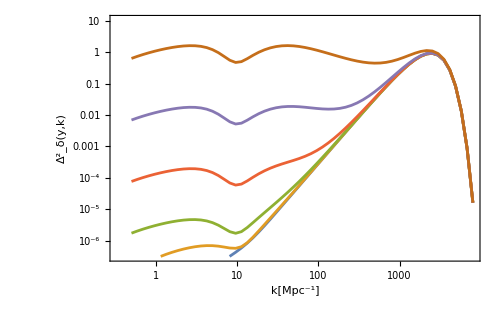

```mathematica
(*~~~~~~~ Power Spectrum Evolution ~~~~~~~*)


(* setting up initial conditions *)
dy=(r midpts)/(√(1+midpts)); (* integration measure *)
kk=klist; (*extract k values *)
PisoIn[j_]:=kk[[j]]^3/(2 π^2)π^(3/2)/ks^3 E^((-kk[[j]]^2)/(4 ks^2)); (* time-independent isocurvature spectrum "initial" *)
PR[j_]:=2 10^-9(36(3+Log[0.15 kk[[j]]/keq]-Log[4/y0])^2); (* the initial subhorizon adiabatic spectrum*)
dlnPdlny[j_]:=2/(3+Log[0.15 kk[[j]]/keq]-Log[4/y0]); (* log y derivative of the initial adiabatic spectrum *)


(* evolution *)
PowerSpectra=Table[Module[{i0,PSY},i0=Nearest[midpts->"Index",Y][[1]];
PSY=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]],Tc=results[[j,4]]}, (* First T^(a,b,c) are extracted from results and then the PS evolution is constructed *)PisoIn[j](1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]]))) (* iso PS evolution *)
+PR[j](Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j] Tb[[i0,1]])^2(* ad PS evolution *)
],{j,Length[results]}];
{midpts[[i0]],PSY}],{Y,yout}];

(* plot *)
TotalPS=ListLogLogPlot[Table[Transpose[{kk,PowerSpectra[[j,2]]}],{j,Length[yout]}],Joined->True,Frame->True, FrameLabel->{"k[Mpc^-1]","(Δ^2)_δ(y,k)"},FrameStyle->15,PlotRange->{10^-6.5,10.5},ImageSize->500]
```